```mathematica
initial={0.005,0.01,0.025,0.05,0.1};
paraset=Import[FileNameJoin[{NotebookDirectory[],"paraset.csv"}]];
```

```mathematica
cellratiosum1={};
cellratiosum2={};
mixratiosum1={};
mixratiosum2={};
mixratioallsum1={};
mixratioallsum2={};
Giniratiosum1={};
Giniratiosum2={};
Giniratioallsum1={};
Giniratioallsum2={};
Moransum1={};
Moransum2={};
typelist1={};
typelist2={};
mixtypelist1={};
mixtypelist2={};
rationsumall1={};
rationsumall2={};
Do[
Ginimove=Transpose@Table[Flatten@Take[Import[FileNameJoin[{NotebookDirectory[],"move",ToString@initial[[i]],"Cellgro-"<>ToString@j<>".csv"}]],All,{2}],{j,1,8}];
GiniQS=Transpose@Table[Flatten@Take[Import[FileNameJoin[{NotebookDirectory[],"QS",ToString@initial[[i]],"Cellgro-"<>ToString@j<>".csv"}]],All,{2}],{j,1,8}];
Gininotmove=Transpose@Table[Flatten@Take[Import[FileNameJoin[{NotebookDirectory[],"notmove",ToString@initial[[i]],"Cellgro-"<>ToString@j<>".csv"}]],All,{2}],{j,1,8}];
Giniratio1=Ginimove/Gininotmove;
Giniratioallsum1=Join[Giniratioallsum1,{Giniratio1}];
Giniratiomean1=Mean[Transpose[Giniratio1]];
Giniratio2=GiniQS/Gininotmove;
Giniratioallsum2=Join[Giniratioallsum2,{Giniratio2}];
Giniratiomean2=Mean[Transpose[Giniratio2]];
Giniratiosum1=Join[Giniratiosum1,{Giniratiomean1}];
Giniratiosum2=Join[Giniratiosum2,{Giniratiomean2}];

Cellmove=Transpose@Table[Flatten@Take[Import[FileNameJoin[{NotebookDirectory[],"move",ToString@initial[[i]],"Cellgro-"<>ToString@j<>".csv"}]],All,{1}],{j,1,8}];
CellQS=Transpose@Table[Flatten@Take[Import[FileNameJoin[{NotebookDirectory[],"QS",ToString@initial[[i]],"Cellgro-"<>ToString@j<>".csv"}]],All,{1}],{j,1,8}];
Cellnotmove=Transpose@Table[Flatten@Take[Import[FileNameJoin[{NotebookDirectory[],"notmove",ToString@initial[[i]],"Cellgro-"<>ToString@j<>".csv"}]],All,{1}],{j,1,8}];
cellratio1=Cellmove/Cellnotmove;
cellratiomean1=Mean[Transpose[cellratio1]];
cellratio2=CellQS/Cellnotmove;
cellratiomean2=Mean[Transpose[cellratio2]];
cellratiosum1=Join[cellratiosum1,{cellratiomean1}];
cellratiosum2=Join[cellratiosum2,{cellratiomean2}];
rationsumall1=Join[rationsumall1,{cellratio1}];
rationsumall2=Join[rationsumall2,{cellratio2}];

testdata1={};
testdata2={};
Do[
test1=MannWhitneyTest[{Cellmove[[k]],Cellnotmove[[k]]}];
testdata1=Join[testdata1,{{cellratiomean1[[k]],test1}}];
test2=MannWhitneyTest[{CellQS[[k]],Cellnotmove[[k]]}];
testdata2=Join[testdata2,{{cellratiomean2[[k]],test2}}];
,{k,1,300}];
movetype1=Select[testdata1,#[[1]]>1&&#[[2]]<0.05&];
movetype2=Select[testdata1,#[[2]]>0.05&];
movetype3=Select[testdata1,#[[1]]<1&&#[[2]]<0.05&];
QStype1=Select[testdata2,#[[1]]>1&&#[[2]]<0.05&];
QStype2=Select[testdata2,#[[2]]>0.05&];
QStype3=Select[testdata2,#[[1]]<1&&#[[2]]<0.05&];
typelist1=Join[typelist1,{{Length@movetype1,Length@movetype2,Length@movetype3}}];
typelist2=Join[typelist2,{{Length@QStype1,Length@QStype2,Length@QStype3}}];


mixingmove=Transpose@Table[Flatten@Import[FileNameJoin[{NotebookDirectory[],"move",ToString@initial[[i]],"mixing-"<>ToString@j<>".csv"}]],{j,1,8}];
mixingQS=Transpose@Table[Flatten@Import[FileNameJoin[{NotebookDirectory[],"QS",ToString@initial[[i]],"mixing-"<>ToString@j<>".csv"}]],{j,1,8}];
mixingnotmove=Transpose@Table[Flatten@Import[FileNameJoin[{NotebookDirectory[],"notmove",ToString@initial[[i]],"mixing-"<>ToString@j<>".csv"}]],{j,1,8}];
mixratio1=mixingmove/mixingnotmove;
mixratio1=Table[(mixratio1[[j]]/Mean[Flatten@mixratio1])*(cellratiomean1[[j]])^(1/2),{j,1,Length@cellratiomean1}];
If[i==1,mixratio1=mixratio1+0.2];
mixratiomean1=Mean[Transpose[mixratio1]];
mixratioallsum1=Join[mixratioallsum1,{mixratio1}];
mixratio2=mixingQS/mixingnotmove;
mixratio2=Table[(mixratio2[[j]]/Mean[Flatten@mixratio2])*(cellratiomean2[[j]])^(1/2),{j,1,Length@cellratiomean2}];
If[i==1,mixratio2=mixratio2+0.2];
mixratioallsum2=Join[mixratioallsum2,{mixratio2}];
mixratiomean2=Mean[Transpose[mixratio2]];
mixratiosum1=Join[mixratiosum1,{mixratiomean1}];
mixratiosum2=Join[mixratiosum2,{mixratiomean2}];

testdata1={};
testdata2={};
Do[
test1=MannWhitneyTest[{mixingmove[[k]],mixingnotmove[[k]]}];
testdata1=Join[testdata1,{{mixratiomean1[[k]],test1}}];
test2=MannWhitneyTest[{CellQS[[k]],Cellnotmove[[k]]}];
testdata2=Join[testdata2,{{mixratiomean2[[k]],test2}}];
,{k,1,300}];
movetype1=Select[testdata1,#[[1]]>1&&#[[2]]<0.05&];
movetype2=Select[testdata1,#[[2]]>0.05&];
movetype3=Select[testdata1,#[[1]]<1&&#[[2]]<0.05&];
QStype1=Select[testdata2,#[[1]]>1&&#[[2]]<0.05&];
QStype2=Select[testdata2,#[[2]]>0.05&];
QStype3=Select[testdata2,#[[1]]<1&&#[[2]]<0.05&];
mixtypelist1=Join[mixtypelist1,{{Length@movetype1,Length@movetype2,Length@movetype3}}];
mixtypelist2=Join[mixtypelist2,{{Length@QStype1,Length@QStype2,Length@QStype3}}];



matrixmove=Transpose@Table[Flatten@Take[Import[FileNameJoin[{NotebookDirectory[],"move",ToString@initial[[i]],"Matrix-"<>ToString@j<>".csv"}]],All,{3}],{j,1,8}];
matrixQS=Transpose@Table[Flatten@Take[Import[FileNameJoin[{NotebookDirectory[],"QS",ToString@initial[[i]],"Matrix-"<>ToString@j<>".csv"}]],All,{3}],{j,1,8}];
matrixnotmove=Transpose@Table[Flatten@Take[Import[FileNameJoin[{NotebookDirectory[],"notmove",ToString@initial[[i]],"Matrix-"<>ToString@j<>".csv"}]],All,{3}],{j,1,8}];
Moransum1=Join[Moransum1,{{Flatten@matrixnotmove,Flatten@matrixmove,Flatten@matrixQS}}];

matrixmove=Transpose@Table[Flatten@Take[Import[FileNameJoin[{NotebookDirectory[],"move",ToString@initial[[i]],"Matrix-"<>ToString@j<>".csv"}]],All,{4}],{j,1,8}];
matrixQS=Transpose@Table[Flatten@Take[Import[FileNameJoin[{NotebookDirectory[],"QS",ToString@initial[[i]],"Matrix-"<>ToString@j<>".csv"}]],All,{4}],{j,1,8}];
matrixnotmove=Transpose@Table[Flatten@Take[Import[FileNameJoin[{NotebookDirectory[],"notmove",ToString@initial[[i]],"Matrix-"<>ToString@j<>".csv"}]],All,{4}],{j,1,8}];
Moransum2=Join[Moransum2,{{Flatten@matrixnotmove,Flatten@matrixmove,Flatten@matrixQS}}];

,{i,1,5}];
```

```mathematica
freplot1=BarChart[typelist1,ChartLayout->"Stacked",ImageSize->500,AspectRatio->0.75,
ChartStyle->95,Frame->True,FrameStyle->Directive[Thickness[0.008],Black,24],BarSpacing->{0,0.5},Axes->False]
freplot2=BarChart[typelist2,ChartLayout->"Stacked",ImageSize->500,AspectRatio->0.75,
ChartStyle->95,Frame->True,FrameStyle->Directive[Thickness[0.008],Black,24],BarSpacing->{0,0.5},Axes->False]
Export[FileNameJoin[{NotebookDirectory[],"plot-SC","freplot1.eps"}],freplot1];
Export[FileNameJoin[{NotebookDirectory[],"plot-SC","freplot2.eps"}],freplot2];
```

```mathematica
mixfreplot1=BarChart[mixtypelist1,ChartLayout->"Stacked",ImageSize->500,AspectRatio->0.75,
ChartStyle->95,Frame->True,FrameStyle->Directive[Thickness[0.008],Black,24],BarSpacing->{0,0.5},Axes->False]
mixfreplot2=BarChart[mixtypelist2,ChartLayout->"Stacked",ImageSize->500,AspectRatio->0.75,
ChartStyle->95,Frame->True,FrameStyle->Directive[Thickness[0.008],Black,24],BarSpacing->{0,0.5},Axes->False]
Export[FileNameJoin[{NotebookDirectory[],"plot-SC","mixfreplot1.eps"}],mixfreplot1];
Export[FileNameJoin[{NotebookDirectory[],"plot-SC","mixfreplot2.eps"}],mixfreplot2];
```

```mathematica
PGdis1=DistributionChart[Moransum1,ImageSize->500,AspectRatio->0.5,PlotRange->{-0.2,1},BarSpacing->{0.2,1},
ChartStyle->ColorData[95],ChartBaseStyle->EdgeForm[Thick],Frame->True,FrameStyle->Directive[Thickness[0.008],Black,24],Axes->False];
PGdis2=DistributionChart[Moransum2,ImageSize->500,AspectRatio->0.5,PlotRange->{-0.2,1},BarSpacing->{0.2,1},
ChartStyle->ColorData[95],ChartBaseStyle->EdgeForm[Thick],Frame->True,FrameStyle->Directive[Thickness[0.008],Black,24],Axes->False];
Export[FileNameJoin[{NotebookDirectory[],"plot-SC","PG1-dis.eps"}],PGdis1];
Export[FileNameJoin[{NotebookDirectory[],"plot-SC","PG2-dis.eps"}],PGdis2];
```

```mathematica
SCGv1=DistributionChart[Log10@Giniratiosum1,ImageSize->500,AspectRatio->0.75,PlotRange->{-3,2},
ChartStyle->ColorData[95],ChartBaseStyle->EdgeForm[Thick],Frame->True,FrameStyle->Directive[Thickness[0.008],Black,24],Axes->False];
SCGv2=DistributionChart[Log10@Giniratiosum2,ImageSize->500,AspectRatio->0.75,PlotRange->{-3,2},
ChartStyle->ColorData[95],ChartBaseStyle->EdgeForm[Thick],Frame->True,FrameStyle->Directive[Thickness[0.008],Black,24],Axes->False];
Export[FileNameJoin[{NotebookDirectory[],"plot-SC","SCGv1.eps"}],SCGv1];
Export[FileNameJoin[{NotebookDirectory[],"plot-SC","SCGv2.eps"}],SCGv2];
```

```mathematica
SCG1=DistributionChart[Log10@cellratiosum1,ImageSize->500,AspectRatio->0.75,PlotRange->{-1,1.2},
ChartStyle->ColorData[95],ChartBaseStyle->EdgeForm[Thick],Frame->True,FrameStyle->Directive[Thickness[0.008],Black,24],Axes->False];
SCG2=DistributionChart[Log10@cellratiosum2,ImageSize->500,AspectRatio->0.75,PlotRange->{-1,1.2},
ChartStyle->ColorData[95],ChartBaseStyle->EdgeForm[Thick],Frame->True,FrameStyle->Directive[Thickness[0.008],Black,24],Axes->False];
Export[FileNameJoin[{NotebookDirectory[],"plot-SC","SCG1.eps"}],SCG1];
Export[FileNameJoin[{NotebookDirectory[],"plot-SC","SCG2.eps"}],SCG2];
```

FittedModel[…]

0.834818

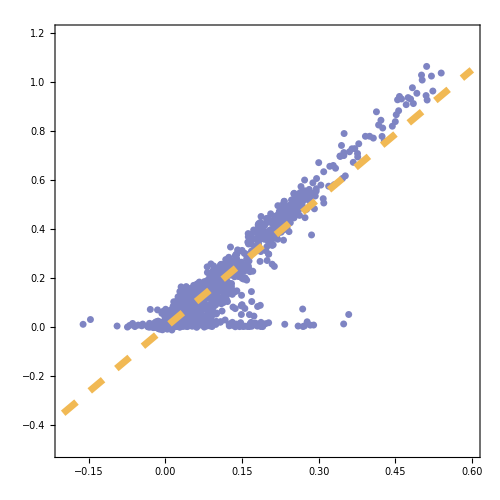

2.51759×10^-25

FittedModel[…]

0.616932

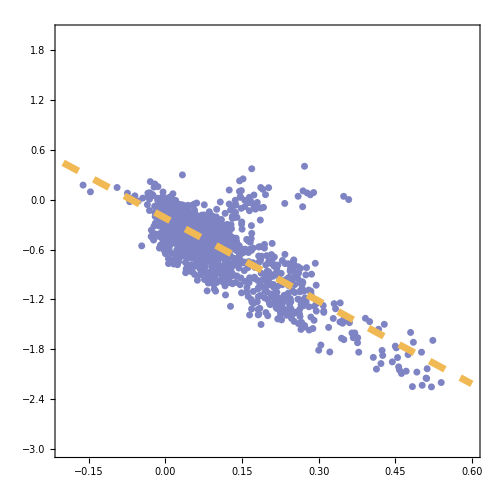

```mathematica
fitdata1=Transpose@Join[{Log10@Flatten@mixratiosum1},{Log10@Flatten@cellratiosum1}];
fit1=LinearModelFit[fitdata1,x,x]
fit1["AdjustedRSquared"]
fitplot1=Show[ListPlot[fitdata1,ImageSize->500,AspectRatio->1,PlotRange->{{-0.2,0.6},{-0.5,1.2}},
PlotStyle->{Directive[PointSize[0.01],RGBColor[126/255,132/255,195/255]]},Frame->True,FrameStyle->Directive[Thickness[0.008],Black,24],Axes->False],Plot[fit1[x],{x,-0.2,0.6},PlotStyle->{Thickness[0.01],RGBColor[241/255,185/255,84/255],Dashing[0.025]}]]
CorrelationTest[Transpose@Join[{Log10@mixratiosum1[[1]]},{Log10@cellratiosum1[[1]]}]]

fitdata2=Transpose@Join[{Log10@Flatten@mixratiosum1},{Log10@Flatten@Giniratiosum1}];
fit2=LinearModelFit[fitdata2,x,x]
fit2["AdjustedRSquared"]
fitplot2=Show[ListPlot[fitdata2,ImageSize->500,AspectRatio->1,PlotRange->{{-0.2,0.6},{-3,2}},
PlotStyle->{Directive[PointSize[0.01],RGBColor[126/255,132/255,195/255]]},Frame->True,FrameStyle->Directive[Thickness[0.008],Black,24],Axes->False],Plot[fit2[x],{x,-0.2,0.6},PlotStyle->{Thickness[0.01],RGBColor[241/255,185/255,84/255],Dashing[0.025]}]]
CorrelationTest[Transpose@Join[{Log10@mixratiosum1[[1]]},{Log10@Giniratiosum1[[1]]}]];
Export[FileNameJoin[{NotebookDirectory[],"plot-SC","mix-ratiofit.eps"}],fitplot1];
Export[FileNameJoin[{NotebookDirectory[],"plot-SC","mix-varafit.eps"}],fitplot2];
```

FittedModel[…]

0.814001

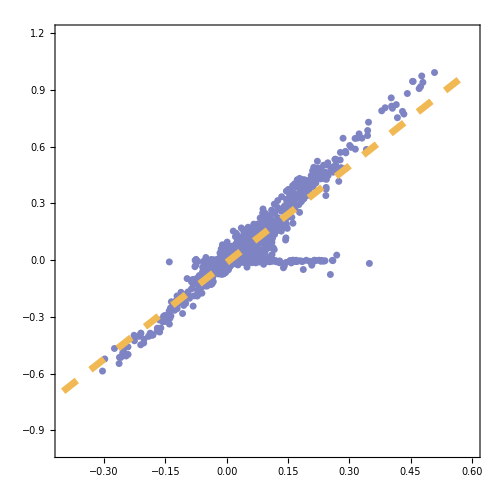

2.51759×10^-25

FittedModel[…]

0.683095

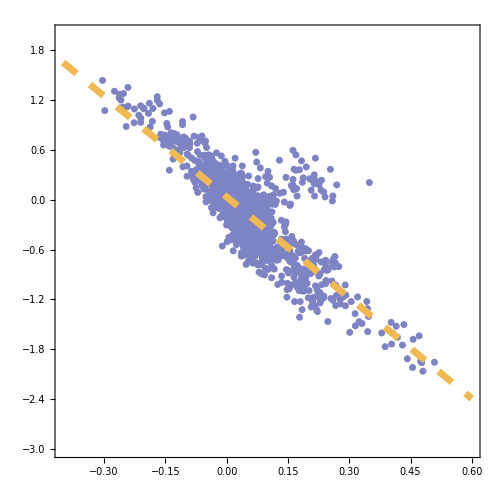

```mathematica
fitdata1=Transpose@Join[{Log10@Flatten@mixratiosum2},{Log10@Flatten@cellratiosum2}];
fit1=LinearModelFit[fitdata1,x,x]
fit1["AdjustedRSquared"]
fitplot1=Show[ListPlot[fitdata1,ImageSize->500,AspectRatio->1,PlotRange->{{-0.4,0.6},{-1,1.2}},
PlotStyle->{Directive[PointSize[0.01],RGBColor[126/255,132/255,195/255]]},Frame->True,FrameStyle->Directive[Thickness[0.008],Black,24],Axes->False],Plot[fit1[x],{x,-0.4,0.6},PlotStyle->{Thickness[0.01],RGBColor[241/255,185/255,84/255],Dashing[0.025]}]]
CorrelationTest[Transpose@Join[{Log10@mixratiosum1[[1]]},{Log10@cellratiosum1[[1]]}]]

fitdata2=Transpose@Join[{Log10@Flatten@mixratiosum2},{Log10@Flatten@Giniratiosum2}];
fit2=LinearModelFit[fitdata2,x,x]
fit2["AdjustedRSquared"]
fitplot2=Show[ListPlot[fitdata2,ImageSize->500,AspectRatio->1,PlotRange->{{-0.4,0.6},{-3,2}},
PlotStyle->{Directive[PointSize[0.01],RGBColor[126/255,132/255,195/255]]},Frame->True,FrameStyle->Directive[Thickness[0.008],Black,24],Axes->False],Plot[fit2[x],{x,-0.4,0.6},PlotStyle->{Thickness[0.01],RGBColor[241/255,185/255,84/255],Dashing[0.025]}]]
CorrelationTest[Transpose@Join[{Log10@mixratiosum1[[1]]},{Log10@Giniratiosum1[[1]]}]];
Export[FileNameJoin[{NotebookDirectory[],"plot-SC","mix-ratiofit-agg.eps"}],fitplot1];
Export[FileNameJoin[{NotebookDirectory[],"plot-SC","mix-varafit-agg.eps"}],fitplot2];
```

```mathematica
DistributionChart[Log10@mixratiosum1,ImageSize->500,AspectRatio->0.75,PlotRange->{-0.4,0.6},
ChartStyle->ColorData[95],ChartBaseStyle->EdgeForm[Thick],Frame->True,FrameStyle->Directive[Thickness[0.008],Black,24],Axes->False];
DistributionChart[Log10@mixratiosum2,ImageSize->500,AspectRatio->0.75,PlotRange->{-0.4,0.6},
ChartStyle->ColorData[95],ChartBaseStyle->EdgeForm[Thick],Frame->True,FrameStyle->Directive[Thickness[0.008],Black,24],Axes->False];
DistributionChart[Log10@Giniratiosum1,ImageSize->500,AspectRatio->0.75,PlotRange->{-3,2},
ChartStyle->ColorData[95],ChartBaseStyle->EdgeForm[Thick],Frame->True,FrameStyle->Directive[Thickness[0.008],Black,24],Axes->False]
DistributionChart[Log10@Giniratiosum2,ImageSize->500,AspectRatio->0.75,PlotRange->{-3,2},
ChartStyle->ColorData[95],ChartBaseStyle->EdgeForm[Thick],Frame->True,FrameStyle->Directive[Thickness[0.008],Black,24],Axes->False]
```

```mathematica
fitdata1=Transpose@Join[{Log10@mixratiosum1[[1]]},{Log10@cellratiosum1[[1]]}];
fit1=LinearModelFit[fitdata1,x,x]
fit1["AdjustedRSquared"]
Show[ListPlot[fitdata1,ImageSize->500,AspectRatio->1,PlotRange->{{0.2,0.5},{-0.2,1.2}},
PlotStyle->ColorData[95],Frame->True,FrameStyle->Directive[Thickness[0.008],Black,24],Axes->False],Plot[fit1[x],{x,0,0.5},PlotStyle->{Thickness[0.01],ColorData[95][2],Dashing[0.025]}]]
CorrelationTest[Transpose@Join[{Log10@mixratiosum1[[1]]},{Log10@cellratiosum1[[1]]}]]
```